## Fitting sigma dan eden

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\efpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\efpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\efpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\efpc_gup1E-9.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP2.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
(* inverted data! *)
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup2E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\efpc_gup2E-7.dat

### Memisahkan data σ (= Pr-Pt) vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\sfpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\sfpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\sfpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\sfpc_gup1E-9.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_BSPB_GUP2.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup2E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-06-18_parset_corrected\fitting\sfpc_gup2E-7.dat

### fitting anisotropik

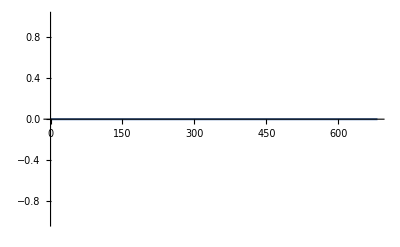

0.

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*),PlotRange->Full]
```

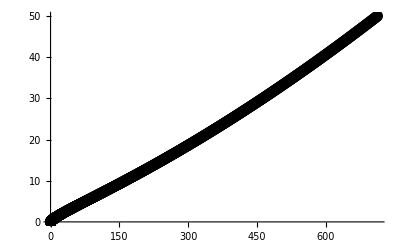

0.12056837552387968 + 0.07688401244766364*P0 - 
     -  0.0002276286297179068*P0**2 + 1.150324384979878e-6*P0**3 - 
     -  2.638361922018149e-9*P0**4 + 2.9552627363262106e-12*P0**5 - 
     -  1.285592642364798e-15*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

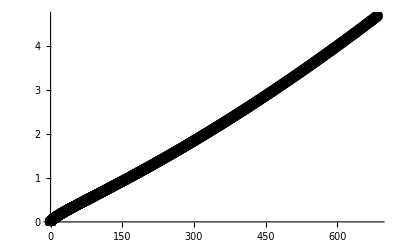

0.015913128640437913 + 0.007740662593776933*P0 - 
     -  0.000024896024805009704*P0**2 + 
     -  1.2915291370409624e-7*P0**3 - 3.0832965844491094e-10*P0**4 + 
     -  3.597354418274768e-13*P0**5 - 1.6301667873403833e-16*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

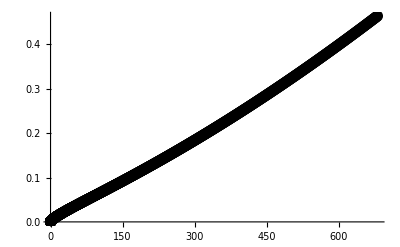

0.0016283169270510053 + 0.0007748327444547611*P0 - 
     -  2.5171222962853955e-6*P0**2 + 1.3107604797043123e-8*P0**3 - 
     -  3.1458758723624496e-11*P0**4 + 3.690249269750217e-14*P0**5 - 
     -  1.6813494837513086e-17*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

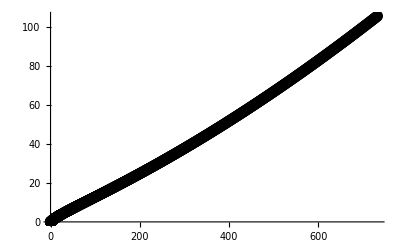

0.1504731016301074 + 0.1531753943386649*P0 - 
     -  0.00042246801549288937*P0**2 + 2.1058529378548e-6*P0**3 - 
     -  4.697863851274443e-9*P0**4 + 5.115630837060703e-12*P0**5 - 
     -  2.1635443413010636e-15*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup2E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

### fitting energy density GUP 0E0

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 0E0 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

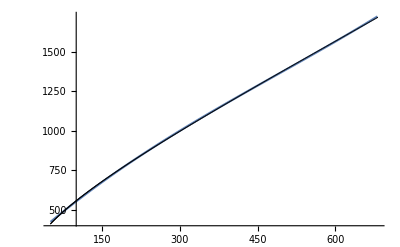

282.077+2.92924 P0-0.00224573 P0^2+1.54121×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP0E0=fitted
```

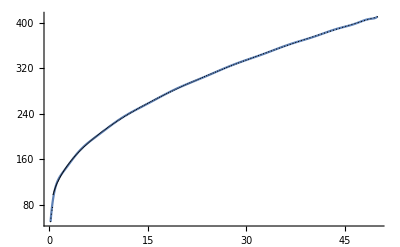

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP0E0=fitted;
```

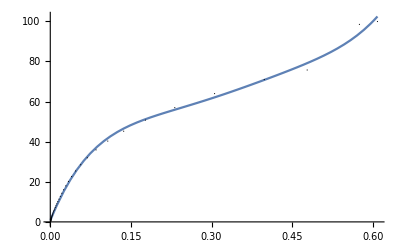

0.628228+667.714 P0-3654.22 P0^2+10990.6 P0^3-15987. P0^4+9157.73 P0^5

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP0E0=fitted
```

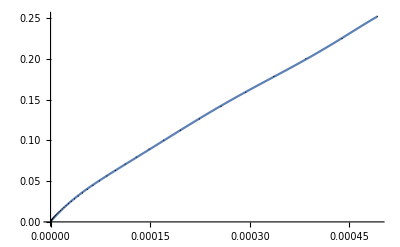

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP0E0=fitted
```

#### Cek hasilnya

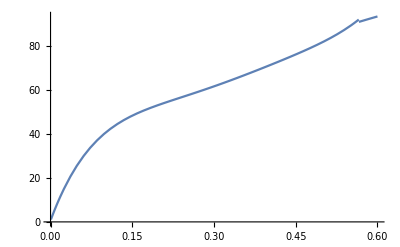

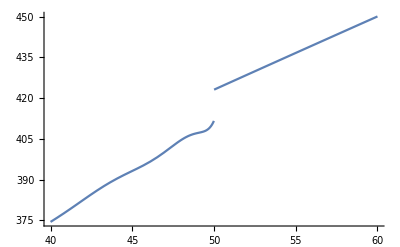

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP0E0;
FED2[P0_]=fitOuterCoreGUP0E0;
FED3[P0_]=fitInnerCrustGUP0E0;
FED4[P0_]=fitOuterCrustGUP0E0;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP0E0//FortranForm
```

282.07731725854666 + 2.929240449172745*P0 - 
     -  0.0022457325058573845*P0**2 + 1.5412122617046955e-6*P0**3

```mathematica
fitOuterCoreGUP0E0//FortranForm
```

21.741216538741387 + 185.2377435926766*P0 - 
     -  144.30597578798978*P0**2 + 67.96738590262504*P0**3 - 
     -  19.85098051038415*P0**4 + 3.845817630385478*P0**5 - 
     -  0.519250711264411*P0**6 + 0.05057512872318498*P0**7 - 
     -  0.0036381455995991366*P0**8 + 
     -  0.00019620117398059272*P0**9 - 
     -  7.99340415788295e-6*P0**10 + 
     -  2.4619154915079735e-7*P0**11 - 
     -  5.692597599615043e-9*P0**12 + 
     -  9.718892272129773e-11*P0**13 - 
     -  1.187776627031915e-12*P0**14 + 
     -  9.82465368862169e-15*P0**15 - 
     -  4.925081141753808e-17*P0**16 + 
     -  1.1295132746663252e-19*P0**17

```mathematica
fitInnerCrustGUP0E0//FortranForm
```

0.6282277465136216 + 667.7140088632083*P0 - 
     -  3654.217177967456*P0**2 + 10990.590391758089*P0**3 - 
     -  15987.00403639022*P0**4 + 9157.73481683087*P0**5

```mathematica
fitOuterCrustGUP0E0//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em7 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

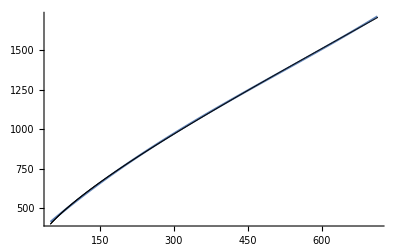

277.729+2.83763 P0-0.00215447 P0^2+1.40357×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em7=fitted
```

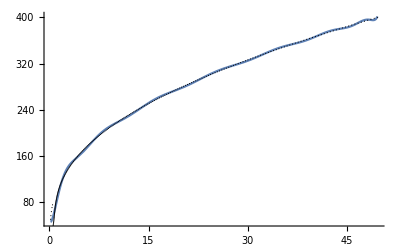

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em7=fitted;
```

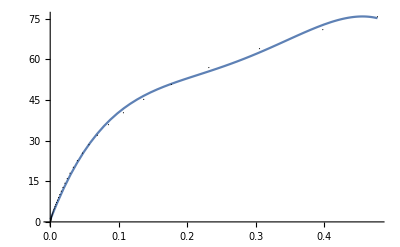

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em7=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

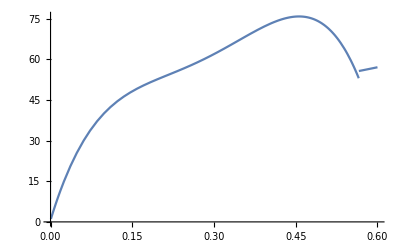

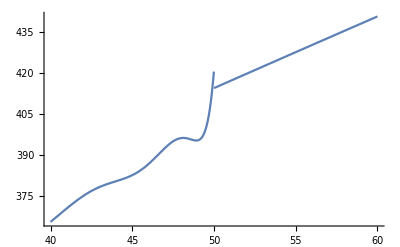

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em7;
FED2[P0_]=fitOuterCoreGUP1Em7;
FED3[P0_]=fitInnerCrustGUP1Em7;
FED4[P0_]=fitOuterCrustGUP1Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em7//FortranForm
```

277.7291096712397 + 2.8376327013933604*P0 - 
     -  0.002154466298162622*P0**2 + 1.4035711959292972e-6*P0**3

```mathematica
fitOuterCoreGUP1Em7//FortranForm
```

48.05621152924977 - 26.24586960162063*P0 + 
     -  98.59336294229816*P0**2 - 59.73053805197146*P0**3 + 
     -  18.665093223307313*P0**4 - 3.594182668221451*P0**5 + 
     -  0.4632180900782332*P0**6 - 0.04190998142633307*P0**7 + 
     -  0.002740503490610357*P0**8 - 
     -  0.00013169641407261964*P0**9 + 
     -  4.6828618237286395e-6*P0**10 - 
     -  1.228898668640918e-7*P0**11 + 
     -  2.3482752539237856e-9*P0**12 - 
     -  3.1754201508766007e-11*P0**13 + 
     -  2.878294419934291e-13*P0**14 - 
     -  1.5683310786025445e-15*P0**15 + 
     -  3.882280447965985e-18*P0**16

```mathematica
fitInnerCrustGUP1Em7//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 
     -  3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 
     -  7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em7//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em8

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em8 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={(*dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],*)dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

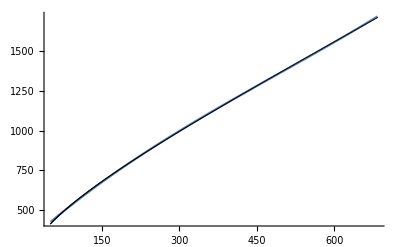

281.378+2.92308 P0-0.00224514 P0^2+1.53504×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em8=fitted
```

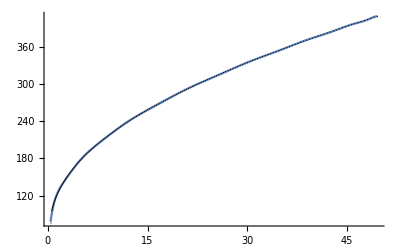

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em8=fitted;
```

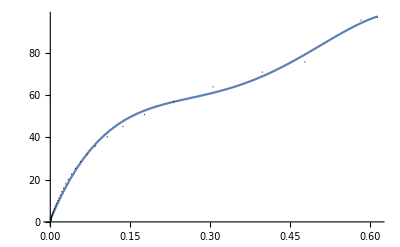

0.930797+604.722 P0-2524.88 P0^2+4857.42 P0^3-3148.65 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em8=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em8=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

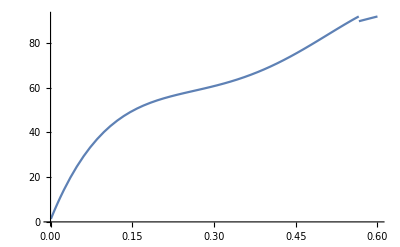

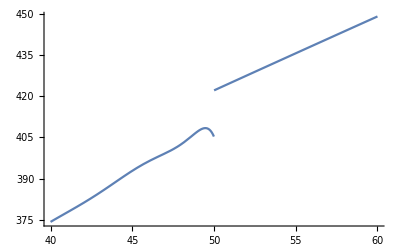

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em8;
FED2[P0_]=fitOuterCoreGUP1Em8;
FED3[P0_]=fitInnerCrustGUP1Em8;
FED4[P0_]=fitOuterCrustGUP1Em8;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em8//FortranForm
```

281.3780851067725 + 2.9230787853388*P0 - 
     -  0.0022451429563034816*P0**2 + 1.5350422400266104e-6*P0**3

```mathematica
fitOuterCoreGUP1Em8//FortranForm
```

36.064244800204605 + 134.41530475418*P0 - 
     -  87.58365870097855*P0**2 + 36.22941303816551*P0**3 - 
     -  9.370463688056223*P0**4 + 1.6075431840293999*P0**5 - 
     -  0.1915264220259657*P0**6 + 0.016365834762859976*P0**7 - 
     -  0.0010245304097275278*P0**8 + 
     -  0.00004756928153784086*P0**9 - 
     -  1.6449193867407531e-6*P0**10 + 
     -  4.217975838535425e-8*P0**11 - 
     -  7.904263035492408e-10*P0**12 + 
     -  1.0511261385076943e-11*P0**13 - 
     -  9.390588156572698e-14*P0**14 + 
     -  5.052124544008177e-16*P0**15 - 1.236615776492197e-18*P0**16

```mathematica
fitInnerCrustGUP1Em8//FortranForm
```

0.9307968604046208 + 604.7222488924658*P0 - 
     -  2524.8772735972398*P0**2 + 4857.421563973808*P0**3 - 
     -  3148.652327034491*P0**4

```mathematica
fitOuterCrustGUP1Em8//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em9

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em9 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

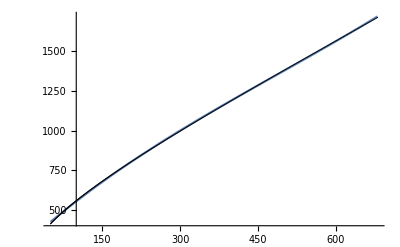

281.929+2.93007 P0-0.00225173 P0^2+1.5474×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em9=fitted
```

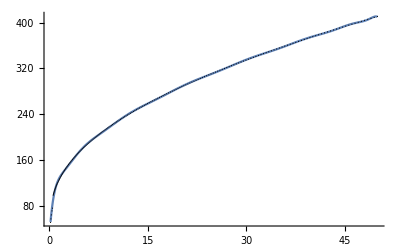

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em9=fitted;
```

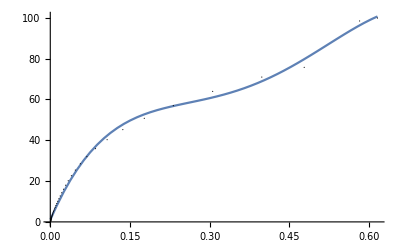

0.925433+605.318 P0-2524.96 P0^2+4823.62 P0^3-3073.41 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em9=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em9=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

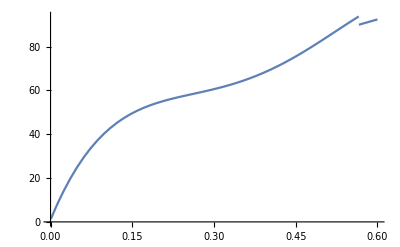

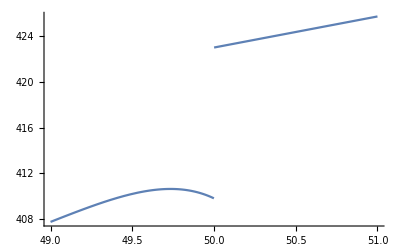

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em9;
FED2[P0_]=fitOuterCoreGUP1Em9;
FED3[P0_]=fitInnerCrustGUP1Em9;
FED4[P0_]=fitOuterCrustGUP1Em9;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,49,51},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em9//FortranForm
```

281.9294734714307 + 2.930065080592614*P0 - 
     -  0.0022517316955908387*P0**2 + 1.5474017486186326e-6*P0**3

```mathematica
fitOuterCoreGUP1Em9//FortranForm
```

25.830610202922383 + 165.43879268020157*P0 - 
     -  116.03388829553688*P0**2 + 49.235701111527604*P0**3 - 
     -  12.879944870321*P0**4 + 2.2206111129000647*P0**5 - 
     -  0.2649566103664792*P0**6 + 0.022625059467465472*P0**7 - 
     -  0.001413410618577376*P0**8 + 
     -  0.00006542371424887345*P0**9 - 
     -  2.2537671813278972e-6*P0**10 + 
     -  5.754305291909604e-8*P0**11 - 
     -  1.0732398448836963e-9*P0**12 + 
     -  1.4200291747537256e-11*P0**13 - 
     -  1.2619166495092905e-13*P0**14 + 
     -  6.751756157806669e-16*P0**15 - 
     -  1.6432653803273405e-18*P0**16

```mathematica
fitInnerCrustGUP1Em9//FortranForm
```

0.9254328183379066 + 605.3175023433296*P0 - 
     -  2524.955605659138*P0**2 + 4823.6241443050685*P0**3 - 
     -  3073.4107136582707*P0**4

```mathematica
fitOuterCrustGUP1Em9//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 2Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em7 + Crust CAREFUL data MAYBE inverted

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup2E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
(*data1=data;
data1=0*data1;
Do[data1[[i]]= data1[[i]]+data[[Length[data]+1-i]];,{i,1,Length[data]}]
data=data1;*)
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

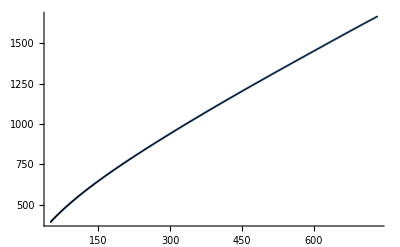

218.321+4.01591 P0-0.0117763 P0^2+0.0000353974 P0^3-6.18288×10^-8 P0^4+5.68755×10^-11 P0^5-2.12379×10^-14 P0^6

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP2Em7=fitted
```

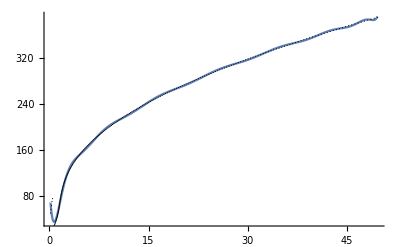

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP2Em7=fitted;
```

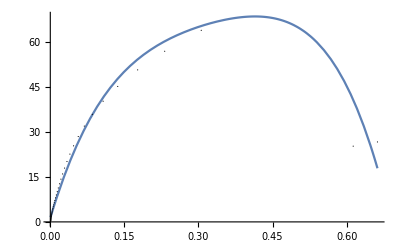

1.30977+547.905 P0-1975.44 P0^2+3742.45 P0^3-2946.35 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP2Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP2Em7=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

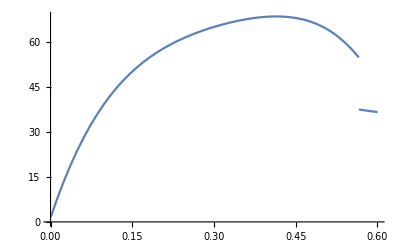

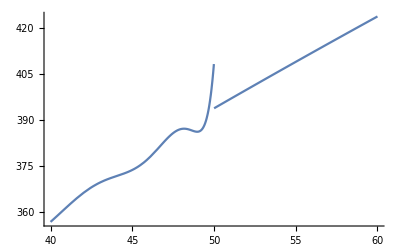

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP2Em7;
FED2[P0_]=fitOuterCoreGUP2Em7;
FED3[P0_]=fitInnerCrustGUP2Em7;
FED4[P0_]=fitOuterCrustGUP2Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP2Em7//FortranForm
```

218.32068878160118 + 4.015913024958688*P0 - 
     -  0.011776262461655017*P0**2 + 0.0000353973566690474*P0**3 - 
     -  6.182882810855576e-8*P0**4 + 
     -  5.6875456246648006e-11*P0**5 - 2.123794027396756e-14*P0**6

```mathematica
fitOuterCoreGUP2Em7//FortranForm
```

101.50653183322409 - 226.48952084624108*P0 + 
     -  260.6622998497509*P0**2 - 123.75879957285153*P0**3 + 
     -  33.73420264153635*P0**4 - 5.922756019262281*P0**5 + 
     -  0.7132973033260214*P0**6 - 0.061252568070193726*P0**7 + 
     -  0.003842110921797544*P0**8 - 
     -  0.00017846394559337169*P0**9 + 
     -  6.1685058551281434e-6*P0**10 - 
     -  1.5803488018994392e-7*P0**11 + 
     -  2.9581544102371806e-9*P0**12 - 
     -  3.928950672071701e-11*P0**13 + 
     -  3.505583338050246e-13*P0**14 - 
     -  1.8836027652129336e-15*P0**15 + 
     -  4.604797030392396e-18*P0**16

```mathematica
fitInnerCrustGUP2Em7//FortranForm
```

1.309770281744584 + 547.9053013628671*P0 - 
     -  1975.4430379992832*P0**2 + 3742.452035699819*P0**3 - 
     -  2946.348916837093*P0**4

```mathematica
fitOuterCrustGUP2Em7//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6